# Kelvin problem in 2-d plane strain

Define the relevant functions that are needed for integrating the response to a point force

```mathematica
x = xo - xs
y = yo - ys
C0 = 1/ (4 * Pi *(1-ν))
r = Sqrt[x^2 + y^2]
g = -C0 * Log[r]
gx = -C0*x/r^2
gy = -C0*y/r^2
ux = fx/(2*μ)*((3-4*ν)*g - x*gx) + fy/(2*μ)*(-y*gx) 
uy = fx/(2*μ)*(-x*gy) + fy/(2*μ)*((3-4*ν)*g -y*gy)
```

xo-xs

yo-ys

1/(4 π (1-ν))

√((xo-xs)^2+(yo-ys)^2)

-Log[√((xo-xs)^2+(yo-ys)^2)]/(4 π (1-ν))

-(xo-xs)/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))

-(yo-ys)/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))

-(fy (xo-xs) (-yo+ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fx ((xo-xs)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

-(fx (-xo+xs) (yo-ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fy ((yo-ys)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

```mathematica
uxmod = ReplaceAll[ux,{ys->0,yo->0}]
uymod = ReplaceAll[uy,{ys->0,yo->0}]
uxint = Integrate[uxmod,{xs,-1,1},Assumptions->{Im[xo]==0}]
uyint = Integrate[uymod,{xs,-1,1},Assumptions->{Im[xo]==0}]
```

(fx (1/(4 π (1-ν))-((3-4 ν) Log[√((xo-xs)^2)])/(4 π (1-ν))))/(2 μ)

-(fy (3-4 ν) Log[√((xo-xs)^2)])/(8 π μ (1-ν))

-(fx (2+1/2 (-3+4 ν) (-4-(-1+xo) Log[(-1+xo)^2]+(1+xo) Log[(1+xo)^2])))/(8 π μ (-1+ν))

(fy (-3+4 ν) (4-2 xo ArcTanh[(2 xo)/(1+xo^2)]+Log[1/((-1+xo^2)^2)]))/(16 π μ (-1+ν))

### First compute indefinite integral and then evaluate at the end points to get definite integral

```mathematica
UXindef = Integrate[ux,xs]
UXdef = ReplaceAll[UXindef,{xs->1}]-ReplaceAll[UXindef,{xs->-1}]
```

1/(16 π μ (1-ν))(-8 fx xs (-1+ν)+8 fx (yo-ys) (-1+ν) ArcTan[(-xo+xs)/(yo-ys)]+fx xs (-3+4 ν) Log[(xo-xs)^2+(yo-ys)^2]+(fy (-yo+ys)+fx xo (3-4 ν)) Log[xo^2-2 xo xs+xs^2+(yo-ys)^2])

1/(16 π μ (1-ν))(-8 fx (-1+ν)+8 fx (yo-ys) (-1+ν) ArcTan[(1-xo)/(yo-ys)]+fx (-3+4 ν) Log[(-1+xo)^2+(yo-ys)^2]+(fy (-yo+ys)+fx xo (3-4 ν)) Log[1-2 xo+xo^2+(yo-ys)^2])-1/(16 π μ (1-ν))(8 fx (-1+ν)+8 fx (yo-ys) (-1+ν) ArcTan[(-1-xo)/(yo-ys)]+(fy (-yo+ys)+fx xo (3-4 ν)) Log[1+2 xo+xo^2+(yo-ys)^2]-fx (-3+4 ν) Log[(1+xo)^2+(yo-ys)^2])

## Check numerical solution versus analytical solution

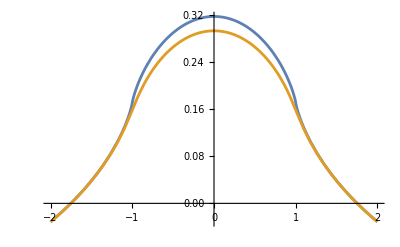

```mathematica
Plot[{ReplaceAll[uxint,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[UXdef,{fx->1,fy->0,μ->1,ν->0.25,ys->0,yo->0.05}]},{xo,-2,2}]
```

## Plot analytical solutions for U_x and U_y

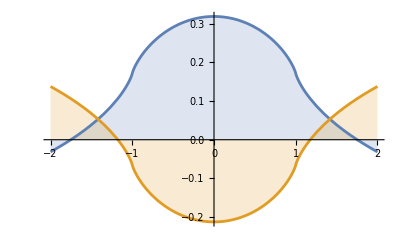

```mathematica
Plot[ {ReplaceAll[uxint,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[uyint,{fx->0,fy -> -1, μ->1,ν->0.25}]},{xo,-2,2},Filling->Axis]
```

## Plot numerical solution for U_x

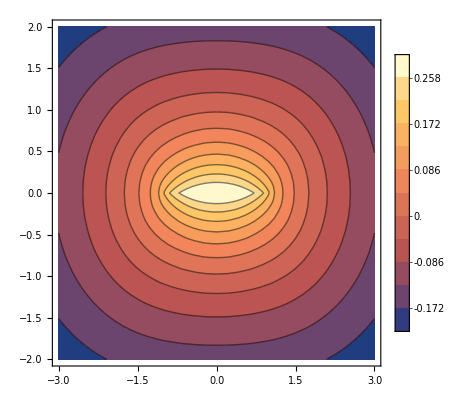

```mathematica
ContourPlot[ReplaceAll[UXdef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->Automatic,Contours->11]
```

## 2-d Numerical Integration

#### Integrate U_x along x_s to get a definite integral, and then compute indefinite integral over y_s, then substitute limits of y_s to get definite integral

```mathematica
UXindef2d =Integrate[UXdef,ys]
```

-1/(16 π μ (-1+ν))(-4 fx (1-xo) (yo-ys) (-1+ν)-4 fx (1+xo) (yo-ys) (-1+ν)-16 fx ys (-1+ν)-4 fx ys (-3+4 ν)+2 fx (1+2 xo+xo^2) (-1+ν) ArcTan[(-1-xo)/(yo-ys)]-2 fx (1-2 xo+xo^2) (-1+ν) ArcTan[(1-xo)/(yo-ys)]-4 fx (yo-ys)^2 (-1+ν) ArcTan[(1-xo)/(yo-ys)]+2 fx (1-2 xo+xo^2) (-1+ν) ArcTan[(-1+xo)/(yo-ys)]-2 fx (1+2 xo+xo^2) (-1+ν) ArcTan[(1+xo)/(yo-ys)]-4 fx (yo-ys)^2 (-1+ν) ArcTan[(1+xo)/(yo-ys)]-2 fy (1-xo) yo ArcTan[(yo-ys)/(1-xo)]+2 (1-xo) (fy yo-fx xo (3-4 ν)) ArcTan[(yo-ys)/(1-xo)]-2 fx (-1+xo) (-3+4 ν) ArcTan[(yo-ys)/(-1+xo)]+2 fy (1+xo) yo ArcTan[(yo-ys)/(1+xo)]-2 (1+xo) (fy yo-fx xo (3-4 ν)) ArcTan[(yo-ys)/(1+xo)]-2 fx (1+xo) (-3+4 ν) ArcTan[(yo-ys)/(1+xo)]+1/2 fy ys^2 Log[(-1+xo)^2+(yo-ys)^2]+(yo-ys) (fy yo-fx xo (3-4 ν)) Log[(-1+xo)^2+(yo-ys)^2]-fx (yo-ys) (-3+4 ν) Log[(-1+xo)^2+(yo-ys)^2]-1/2 fy ys^2 Log[(1+xo)^2+(yo-ys)^2]-(yo-ys) (fy yo-fx xo (3-4 ν)) Log[(1+xo)^2+(yo-ys)^2]-fx (yo-ys) (-3+4 ν) Log[(1+xo)^2+(yo-ys)^2]+1/2 fy (1-xo-yo) (1-xo+yo) Log[1-2 xo+xo^2+yo^2-2 yo ys+ys^2]-1/2 fy (1+xo-yo) (1+xo+yo) Log[1+2 xo+xo^2+yo^2-2 yo ys+ys^2])

1/(32 π μ (-1+ν))(8 fx (1+xo) (-0.5+yo) (-1+ν)-8 fx (1+xo) (0.5+yo) (-1+ν)+32. fx (-1.+ν)-8. fx (-1.+xo) (-0.5+yo) (-1.+ν)+8. fx (-1.+xo) (0.5+yo) (-1.+ν)+fx (-24.+32. ν)+4 fx (-1+xo)^2 (-1+ν) ArcTan[(1-xo)/(-0.5+yo)]+8 fx (-0.5+yo)^2 (-1+ν) ArcTan[(1-xo)/(-0.5+yo)]-4 fx (1+xo)^2 (-1+ν) ArcTan[(-1.-1. xo)/(-0.5+yo)]-4. fx (-1.+xo)^2 (-1.+ν) ArcTan[(-1.+xo)/(-0.5+yo)]+4 fx (1+xo)^2 (-1+ν) ArcTan[(1+xo)/(-0.5+yo)]+8 fx (-0.5+yo)^2 (-1+ν) ArcTan[(1+xo)/(-0.5+yo)]-4. fy (-1.+xo) yo ArcTan[(-0.5+yo)/(1.-1. xo)]+4. (-1.+xo) (fy yo+fx xo (-3.+4. ν)) ArcTan[(-0.5+yo)/(1.-1. xo)]+4 fx (-1+xo) (-3+4 ν) ArcTan[(-0.5+yo)/(-1.+xo)]-4 fy (1+xo) yo ArcTan[(-0.5+yo)/(1+xo)]+4 fx (1+xo) (-3+4 ν) ArcTan[(-0.5+yo)/(1+xo)]+4 (1+xo) (fy yo+fx xo (-3+4 ν)) ArcTan[(-0.5+yo)/(1+xo)]-4 fx (-1+xo)^2 (-1+ν) ArcTan[(1-xo)/(0.5+yo)]-8 fx (0.5+yo)^2 (-1+ν) ArcTan[(1-xo)/(0.5+yo)]+4 fx (1+xo)^2 (-1+ν) ArcTan[(-1.-1. xo)/(0.5+yo)]+4 fx (-1+xo)^2 (-1+ν) ArcTan[(-1.+xo)/(0.5+yo)]-4 fx (1+xo)^2 (-1+ν) ArcTan[(1+xo)/(0.5+yo)]-8 fx (0.5+yo)^2 (-1+ν) ArcTan[(1+xo)/(0.5+yo)]+4. fy (-1.+xo) yo ArcTan[(0.5+yo)/(1.-1. xo)]-4. (-1.+xo) (fy yo+fx xo (-3.+4. ν)) ArcTan[(0.5+yo)/(1.-1. xo)]-4 fx (-1+xo) (-3+4 ν) ArcTan[(0.5+yo)/(-1.+xo)]+4 fy (1+xo) yo ArcTan[(0.5+yo)/(1+xo)]-4 fx (1+xo) (-3+4 ν) ArcTan[(0.5+yo)/(1+xo)]-4 (1+xo) (fy yo+fx xo (-3+4 ν)) ArcTan[(0.5+yo)/(1+xo)]-0.25 fy Log[(-1+xo)^2+(-0.5+yo)^2]+2 fx (-0.5+yo) (-3+4 ν) Log[(-1+xo)^2+(-0.5+yo)^2]-2. (-0.5+yo) (fy yo+fx xo (-3.+4. ν)) Log[(-1.+xo)^2+(-0.5+yo)^2]+0.25 fy Log[(1+xo)^2+(-0.5+yo)^2]+2 fx (-0.5+yo) (-3+4 ν) Log[(1+xo)^2+(-0.5+yo)^2]+2 (-0.5+yo) (fy yo+fx xo (-3+4 ν)) Log[(1+xo)^2+(-0.5+yo)^2]-1. fy (-1.+xo-1. yo) (-1.+xo+yo) Log[1.25+(-2.+xo) xo+(-1.+yo) yo]+fy (1+xo-yo) (1+xo+yo) Log[1.25+xo (2+xo)+(-1.+yo) yo]+0.25 fy Log[(-1+xo)^2+(0.5+yo)^2]-2 fx (0.5+yo) (-3+4 ν) Log[(-1+xo)^2+(0.5+yo)^2]+2 (0.5+yo) (fy yo+fx xo (-3+4 ν)) Log[(-1+xo)^2+(0.5+yo)^2]-0.25 fy Log[(1+xo)^2+(0.5+yo)^2]-2 fx (0.5+yo) (-3+4 ν) Log[(1+xo)^2+(0.5+yo)^2]-2 (0.5+yo) (fy yo+fx xo (-3+4 ν)) Log[(1+xo)^2+(0.5+yo)^2]+fy (-1.+xo-1. yo) (-1.+xo+yo) Log[1.25+(-2.+xo) xo+yo (1.+yo)]-fy (1+xo-yo) (1+xo+yo) Log[1.25+xo (2+xo)+yo (1.+yo)])

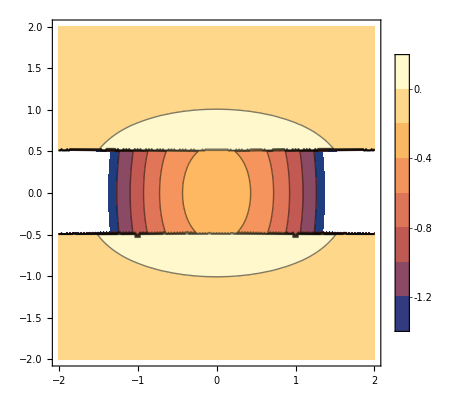

```mathematica
UXdef2d = FullSimplify[ReplaceAll[UXindef2d,{ys->0.5}] - ReplaceAll[UXindef2d,{ys->-0.5}]]
ContourPlot[ReplaceAll[UXdef2d,{fx->1,fy->0,μ->1,ν->0.25}],{xo,-2,2},{yo,-2,2},PlotLegends->Automatic]
```

```mathematica
(*uxint2 = Integrate[Integrate[ux,{xs,-1,1},Assumptions->{Im[xo]==0}],ys, Assumptions->{Im[ys]==0}]*)
(*Integrate[ux,{xs,-1,1},Assumptions->{Im[xo]==0}]*)

(*uxint2 = Integrate[Integrate[ux,{xs,-1,1}],ys]*)
(*uxint2 = Integrate[ux,xs,ys]
uxdefint2 = ReplaceAll[uxint2, {xs->1,ys->0.1}] + ReplaceAll[uxint2, {xs->-1,ys->-0.1}] - ReplaceAll[uxint2, {xs->1,ys->-0.1}] - ReplaceAll[uxint2, {xs->-1,ys->0.1}]*)
```

```mathematica
(*Plot[ReplaceAll[uxdefint2,{fx -> 1,fy ->0,μ->1,ν->0.25,yo->0}],{xo,-2,2}]
ContourPlot[ReplaceAll[uxdefint2,{fx -> 1,fy ->0,μ->1,ν->0.25}],{xo,-2,2},{yo,-2,2}]*)
```